# Airlight Integral Simplification

We’re trying to simplify the “airlight integral” given by the paper as equation 9 : 

	L_a= A_0(T_sv,γ,β)∫_(γ/2)^(π/4+1/2 ArcTan[(T_vp-T_sv Cos[γ])/(T_sv Sin[γ])]) ⅇ^(-A_1(T_sv,γ)Tan[ξ]) ⅆξ

where:
A_0(T_sv,γ,β)=(β^2 I_0 ⅇ^(-T_svCos[γ]))/(2π T_sv Sin[γ])
A_1(T_sv,γ)= T_sv Sin[γ]
T_sv=β D_sv
T_vp=β D_vp
β is the scattering coefficient
D_sv is the distance from the light source s to the view point v
D_vp is the distance from the view point v to the object position p
γ is the angle between the view direction and the light direction

```mathematica
(*ClearAll["Global`*"]*)
Subscript[L, a]= Subscript[A, 0](Subscript[T, sv],γ,β)∫_(γ/2)^(π/4+1/2 ArcTan[(Subscript[T, vp]-Subscript[T, sv] Cos[γ])/(Subscript[T, sv] Sin[γ])]) ⅇ^(-Subscript[A, 1](Subscript[T, sv],γ)Tan[ξ]) ⅆξ
```

The integral in its most basic form is :
F(u,v) = ∫_0^v ⅇ^(-u Tan[ξ])ⅆξ    (10)

There’s no simple analytic expression for (10) as we can see below:

```mathematica
Integrate[ⅇ^(-u Tan[ξ]),ξ]
```

1/2 ⅈ ⅇ^(-ⅈ u) (-ExpIntegralEi[-u (-ⅈ+Tan[ξ])]+ⅇ^(2 ⅈ u) ExpIntegralEi[-u (ⅈ+Tan[ξ])])

The plotting of the numerical integration of F gives:

```mathematica
Clear[F]
F[u_?NumericQ, v_?NumericQ] := NIntegrate[Exp[-u*Tan[ξ]], {ξ,0,v}]
```

```mathematica
Plot3D[F[u, v], {u,0,10},{v, 0, π/2},PlotRange->Full,AxesLabel->{"u","v","F[u,v]"}]
```

-Graphics3D-

Finding an approximation for the curve

We start from the following hypothesis: F[0,v]=v and any curve F[u,v] is of the form F[u,v] = a(v)+b(v) Exp[-c(v)*u^(d(v))]  (1)
The idea is to generate a few curves for specific values of v and find the matching a(v), b(v), c(v) and d(v) for each one. Then we need to find a simple rule linking a,b,c,d depending on u again.
In the end, for any given u, we can analytically retrieve a(u), b(u), c(u) and d(u) and evaluate F[u,v] using eq. (1).

```mathematica
resU = 80; resV = 20;
rangeU=20;
samples=Table[u,{u,1/resU,rangeU,rangeU/resU}]
samplesV = Table[v,{v,π/(2*resV),π/2,π/(2*resV)}]
```

{1/80,21/80,41/80,61/80,81/80,101/80,121/80,141/80,161/80,181/80,201/80,221/80,241/80,261/80,281/80,301/80,321/80,341/80,361/80,381/80,401/80,421/80,441/80,461/80,481/80,501/80,521/80,541/80,561/80,581/80,601/80,621/80,641/80,661/80,681/80,701/80,721/80,741/80,761/80,781/80,801/80,821/80,841/80,861/80,881/80,901/80,921/80,941/80,961/80,981/80,1001/80,1021/80,1041/80,1061/80,1081/80,1101/80,1121/80,1141/80,1161/80,1181/80,1201/80,1221/80,1241/80,1261/80,1281/80,1301/80,1321/80,1341/80,1361/80,1381/80,1401/80,1421/80,1441/80,1461/80,1481/80,1501/80,1521/80,1541/80,1561/80,1581/80}

{π/40,π/20,(3 π)/40,π/10,π/8,(3 π)/20,(7 π)/40,π/5,(9 π)/40,π/4,(11 π)/40,(3 π)/10,(13 π)/40,(7 π)/20,(3 π)/8,(2 π)/5,(17 π)/40,(9 π)/20,(19 π)/40,π/2}

```mathematica
ta=Table[Table[F[u,v],{u,1/resU,rangeU,rangeU/resU}],{v,π/(2*resV),π/2,π/(2*resV)}]; (* Don't start from bad case v=0! *)
```

{π/40,π/20,(3 π)/40,π/10,π/8,(3 π)/20,(7 π)/40,π/5,(9 π)/40,π/4,(11 π)/40,(3 π)/10,(13 π)/40,(7 π)/20,(3 π)/8,(2 π)/5,(17 π)/40,(9 π)/20,(19 π)/40,π/2}

{1.51062,1.0627,0.852206,0.7154,0.617187,0.542649,0.483949,0.436455,0.397222,0.364266,0.336199,0.312016,0.290971,0.272498,0.256158,0.241608,0.228573,0.216832,0.206205,0.196542,0.18772,0.179636,0.172202,0.165345,0.159,0.153113,0.147637,0.142531,0.13776,0.133291,0.129098,0.125156,0.121444,0.117942,0.114632,0.111501,0.108533,0.105718,0.103042,0.100497,0.0980726,0.0957611,0.0935548,0.0914466,0.0894303,0.0875,0.0856503,0.0838765,0.0821739,0.0805383,0.078966,0.0774533,0.075997,0.0745939,0.0732413,0.0719365,0.070677,0.0694604,0.0682848,0.067148,0.0660481,0.0649834,0.0639523,0.0629532,0.0619846,0.0610452,0.0601337,0.0592488,0.0583895,0.0575546,0.056743,0.055954,0.0551864,0.0544396,0.0537125,0.0530046,0.0523149,0.0516429,0.0509879,0.0503492}

20

80

80

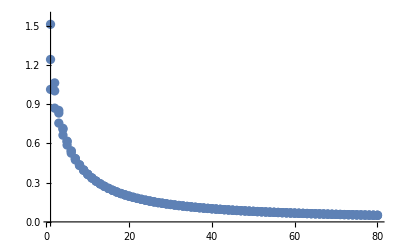

```mathematica
Table[v,{v,π/(2*resV),π/2,π/(2*resV)}]
Table[F[u,π/2],{u,1/resU,rangeU,rangeU/resU}]
Length[ta]
Length[ta[[resV]]]
Length[samples]
Show[ListPlot[ta[[-1]]], ListPlot[ta[[-5]]], ListPlot[ta[[-8]]],PlotRange->{{1,resU},{0,π/2 }},AxesOrigin->{1,0}]
```

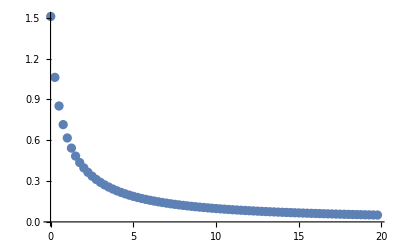

```mathematica
ListPlot[Transpose[{samples,ta[[-1]]}],PlotRange->Full]
```

```mathematica
fittingU=a+b*Exp[-c * u^d];
fitResult0 = FindFit[ta[[-1]],fittingU,{a,b,c,d},u]
```

{a→0.0221365,b→7.214,c→1.58055,d→0.28534}

```mathematica
fitResults0 = Table[FindFit[ta[[v]], fittingU, {a,b,c,d}, u],{v,1,resV-1}];
MatrixForm[fitResults0]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(a→-0.0128553 | b→0.0933335 | c→0.0138067 | d→0.851225
a→0.0862551 | b→2.08325 | c→3.38367 | d→26.7276
a→0.0309245 | b→0.213773 | c→0.0409532 | d→0.928345
a→0.035659 | b→0.296615 | c→0.0583958 | d→0.894278
a→0.0392379 | b→0.384885 | c→0.0783722 | d→0.8601
a→0.0420109 | b→0.479048 | c→0.101079 | d→0.826477
a→0.0441862 | b→0.579872 | c→0.126778 | d→0.793525
a→0.0458879 | b→0.688488 | c→0.155858 | d→0.761075
a→0.0471864 | b→0.806515 | c→0.188878 | d→0.728828
a→0.0481144 | b→0.936263 | c→0.22663 | d→0.696418
a→0.0486755 | b→1.08107 | c→0.270212 | d→0.663448
a→0.0488468 | b→1.24588 | c→0.321159 | d→0.629498
a→0.0485772 | b→1.43823 | c→0.381637 | d→0.594124
a→0.0477809 | b→1.6701 | c→0.45477 | d→0.556849
a→0.0463253 | b→1.96155 | c→0.545197 | d→0.517151
a→0.0440098 | b→2.34844 | c→0.660046 | d→0.474465
a→0.0405372 | b→2.9001 | c→0.810675 | d→0.428218
a→0.0354929 | b→3.76339 | c→1.01544 | d→0.378044
a→0.0285136 | b→5.26087 | c→1.29963 | d→0.324972)

It’s a rather bad fitting trend for most variables it would seem. Also, the first line messes up the trends, let’s try suppressing it...

```mathematica
fitResults1 = Table[FindFit[ta[[v]], fittingU, {a,b,c,d}, u],{v,2,resV}]
MatrixForm[fitResults1]
```

{{a→0.0862551,b→2.08325,c→3.38367,d→26.7276},{a→0.0309245,b→0.213773,c→0.0409532,d→0.928345},{a→0.035659,b→0.296615,c→0.0583958,d→0.894278},{a→0.0392379,b→0.384885,c→0.0783722,d→0.8601},{a→0.0420109,b→0.479048,c→0.101079,d→0.826477},{a→0.0441862,b→0.579872,c→0.126778,d→0.793525},{a→0.0458879,b→0.688488,c→0.155858,d→0.761075},{a→0.0471864,b→0.806515,c→0.188878,d→0.728828},{a→0.0481144,b→0.936263,c→0.22663,d→0.696418},{a→0.0486755,b→1.08107,c→0.270212,d→0.663448},{a→0.0488468,b→1.24588,c→0.321159,d→0.629498},{a→0.0485772,b→1.43823,c→0.381637,d→0.594124},{a→0.0477809,b→1.6701,c→0.45477,d→0.556849},{a→0.0463253,b→1.96155,c→0.545197,d→0.517151},{a→0.0440098,b→2.34844,c→0.660046,d→0.474465},{a→0.0405372,b→2.9001,c→0.810675,d→0.428218},{a→0.0354929,b→3.76339,c→1.01544,d→0.378044},{a→0.0285136,b→5.26087,c→1.29963,d→0.324972},{a→0.0221365,b→7.214,c→1.58055,d→0.28534}}

(a→0.0862551 | b→2.08325 | c→3.38367 | d→26.7276
a→0.0309245 | b→0.213773 | c→0.0409532 | d→0.928345
a→0.035659 | b→0.296615 | c→0.0583958 | d→0.894278
a→0.0392379 | b→0.384885 | c→0.0783722 | d→0.8601
a→0.0420109 | b→0.479048 | c→0.101079 | d→0.826477
a→0.0441862 | b→0.579872 | c→0.126778 | d→0.793525
a→0.0458879 | b→0.688488 | c→0.155858 | d→0.761075
a→0.0471864 | b→0.806515 | c→0.188878 | d→0.728828
a→0.0481144 | b→0.936263 | c→0.22663 | d→0.696418
a→0.0486755 | b→1.08107 | c→0.270212 | d→0.663448
a→0.0488468 | b→1.24588 | c→0.321159 | d→0.629498
a→0.0485772 | b→1.43823 | c→0.381637 | d→0.594124
a→0.0477809 | b→1.6701 | c→0.45477 | d→0.556849
a→0.0463253 | b→1.96155 | c→0.545197 | d→0.517151
a→0.0440098 | b→2.34844 | c→0.660046 | d→0.474465
a→0.0405372 | b→2.9001 | c→0.810675 | d→0.428218
a→0.0354929 | b→3.76339 | c→1.01544 | d→0.378044
a→0.0285136 | b→5.26087 | c→1.29963 | d→0.324972
a→0.0221365 | b→7.214 | c→1.58055 | d→0.28534)

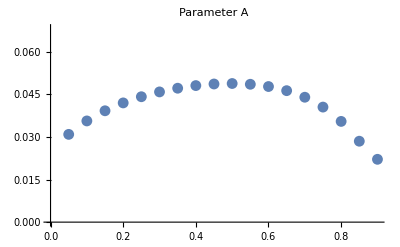

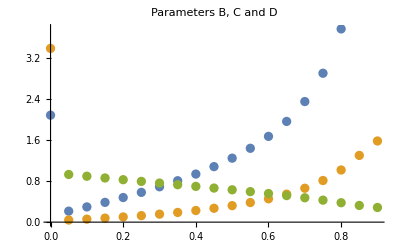

```mathematica
ListPlot[Table[{(i-1)/resV, a/.fitResults1[[i]]},{i,1,resV-1}],PlotLabel->"Parameter A"]
ListPlot[{Table[{(i-1)/resV, b/.fitResults1[[i]]},{i,1,resV-1}],Table[{(i-1)/resV, c/.fitResults1[[i]]},{i,1,resV-1}],Table[{(i-1)/resV, d/.fitResults1[[i]]},{i,1,resV-1}]},PlotLabel->"Parameters B, C and D"]
```

### Changing the fitting curve

Except for parameter a that is not following a monotonic progression, all the other variables seem to behave quite nicely...
Let’s try a more drastic approach by forcing the function to have F[0,v]=v with a new model equation  F[u,v] = v Exp[-a(v)*u^(b(v))]  (2)

```mathematica
Clear[v,fittingU]
fittingU[v_]=v*Exp[-a * Abs[u]^b];
(*fittingU[v_]=v*Exp[-a * Tan[Abs[u]]^b];*)
fitResult1 = FindFit[ta[[-1]],{fittingU[π/2],{a>0,b>0}},{a,b},u]
FindFit[ta[[resV]], fittingU[resV*π/(2*resV)], {a,b}, u,Method->"PrincipalAxis"] (* just checking we really have 20 elements here *)
```

{a→0.318354,b→0.612932}

{a→0.318354,b→0.612932}

1/2 ⅇ^(-a Abs[u]^b) π

{a→0.920097,b→0.49682}

Function[{u},1/2 ⅇ^(-0.920097 Abs[u]^0.49682) π]

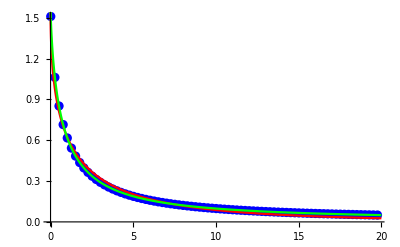

```mathematica
v = resV;
model = fittingU[v*π/(2*resV)]
(*model = a*Exp[-b*u^c]*)
data = Transpose[{samples,ta[[v]]}];
(* data = ta[[v]] *)
pipo = FindFit[data,{model,{a>0,b>0}},{a,b},u ,Method->Automatic]

(*pipo = {a->0.9,b->0.5 } better fit manually! *)

result = Function[{u},Evaluate[model/.pipo]]

Show[
ListPlot[Transpose[{samples,ta[[v]]}],PlotStyle->Blue,PlotRange->Full],
Plot[result[u],{u,0,rangeU},PlotStyle->Red,PlotRange->Full],
Plot[F[u,v*π/(2*resV)],{u,0,rangeU},PlotStyle->Green,PlotRange->Full]]
```

```mathematica
Clear[u,v,fitResults1,fitResult2]
(*v = 9;FindFit[Transpose[{samples,ta[[v]]}], {fittingU[(v-1)*π/(2*resV)],{a>0,b>0}}, {a,b}, u]*)
tempFitResults = Table[FindFit[Transpose[{samples,ta[[v]]}], {fittingU[v*π/(2*resV)],{a>0,b>0}}, {a,b}, u],{v,1,resV}];
(*fitResults1 = Join[{{a->1,b->1}},tempFitResults];*)
fitResults1 =tempFitResults;
MatrixForm[fitResults1]
Length[fitResults1]
```

(a→0.0427249 | b→0.93068
a→0.0904176 | b→0.872025
a→0.140136 | b→0.824497
a→0.189885 | b→0.786177
a→0.238684 | b→0.754838
a→0.286206 | b→0.728613
a→0.332461 | b→0.706101
a→0.377618 | b→0.686267
a→0.421908 | b→0.668357
a→0.465585 | b→0.651804
a→0.5089 | b→0.636176
a→0.552105 | b→0.621133
a→0.59544 | b→0.606398
a→0.63914 | b→0.591742
a→0.683433 | b→0.576971
a→0.728536 | b→0.561921
a→0.774642 | b→0.546464
a→0.82188 | b→0.530527
a→0.870168 | b→0.514183
a→0.920097 | b→0.49682)

20

```mathematica
fittingU[20*π/(2*resV)]/.fitResults1[[20]]
Evaluate[fittingU[20*π/(2*resV)]/.fitResults1[[20]]]/.u->1
fittingU[20*π/(2*resV)]/.fitResults1[[20]]/.u->1
Function[{u},Evaluate[fittingU[20*π/(2*resV)]/.fitResults1[[20]]]]
```

1/2 ⅇ^(-0.920097 Abs[u]^0.49682) π

0.625931

0.625931

Function[{u},1/2 ⅇ^(-0.920097 Abs[u]^0.49682) π]

```mathematica
modelFs=Table[Evaluate[fittingU[v*π/(2*resV)]/.fitResults1][[v]],{v,1,resV}]
```

{1/40 ⅇ^(-0.0427249 Abs[u]^0.93068) π,1/20 ⅇ^(-0.0904176 Abs[u]^0.872025) π,3/40 ⅇ^(-0.140136 Abs[u]^0.824497) π,1/10 ⅇ^(-0.189885 Abs[u]^0.786177) π,1/8 ⅇ^(-0.238684 Abs[u]^0.754838) π,3/20 ⅇ^(-0.286206 Abs[u]^0.728613) π,7/40 ⅇ^(-0.332461 Abs[u]^0.706101) π,1/5 ⅇ^(-0.377618 Abs[u]^0.686267) π,9/40 ⅇ^(-0.421908 Abs[u]^0.668357) π,1/4 ⅇ^(-0.465585 Abs[u]^0.651804) π,11/40 ⅇ^(-0.5089 Abs[u]^0.636176) π,3/10 ⅇ^(-0.552105 Abs[u]^0.621133) π,13/40 ⅇ^(-0.59544 Abs[u]^0.606398) π,7/20 ⅇ^(-0.63914 Abs[u]^0.591742) π,3/8 ⅇ^(-0.683433 Abs[u]^0.576971) π,2/5 ⅇ^(-0.728536 Abs[u]^0.561921) π,17/40 ⅇ^(-0.774642 Abs[u]^0.546464) π,9/20 ⅇ^(-0.82188 Abs[u]^0.530527) π,19/40 ⅇ^(-0.870168 Abs[u]^0.514183) π,1/2 ⅇ^(-0.920097 Abs[u]^0.49682) π}

1/2 ⅇ^(-0.920097 Abs[u]^0.49682) π

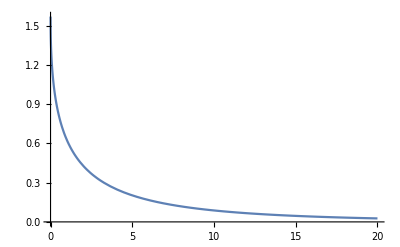

```mathematica
Evaluate[modelFs[[-1]]]
Plot[Evaluate[modelFs[[-1]]],{u,0,rangeU},PlotRange->{0,π/2}]
```

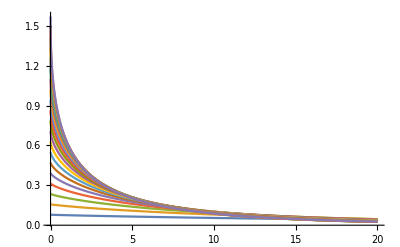

```mathematica
Plot[modelFs,{u,0,rangeU},PlotRange->Full]
```

Finding a best fit for a(v) and b(v)

Now that we have a bunch of well-behaved values for a and b depending on v, we can finally find the functions a(v) and b(v).
Let’s first plot a(v)

```mathematica
finalFitResults = fitResults1;
valuesA = Transpose[{samplesV,a/.finalFitResults}]
valuesB = Transpose[{samplesV,b/.finalFitResults}]
Length[valuesA];
Length[samplesV];
```

{{π/40,0.0427249},{π/20,0.0904176},{(3 π)/40,0.140136},{π/10,0.189885},{π/8,0.238684},{(3 π)/20,0.286206},{(7 π)/40,0.332461},{π/5,0.377618},{(9 π)/40,0.421908},{π/4,0.465585},{(11 π)/40,0.5089},{(3 π)/10,0.552105},{(13 π)/40,0.59544},{(7 π)/20,0.63914},{(3 π)/8,0.683433},{(2 π)/5,0.728536},{(17 π)/40,0.774642},{(9 π)/20,0.82188},{(19 π)/40,0.870168},{π/2,0.920097}}

{{π/40,0.93068},{π/20,0.872025},{(3 π)/40,0.824497},{π/10,0.786177},{π/8,0.754838},{(3 π)/20,0.728613},{(7 π)/40,0.706101},{π/5,0.686267},{(9 π)/40,0.668357},{π/4,0.651804},{(11 π)/40,0.636176},{(3 π)/10,0.621133},{(13 π)/40,0.606398},{(7 π)/20,0.591742},{(3 π)/8,0.576971},{(2 π)/5,0.561921},{(17 π)/40,0.546464},{(9 π)/20,0.530527},{(19 π)/40,0.514183},{π/2,0.49682}}

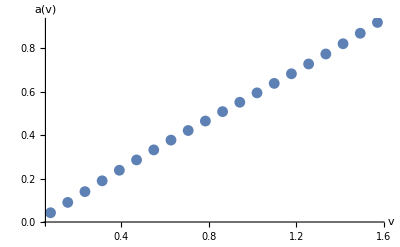

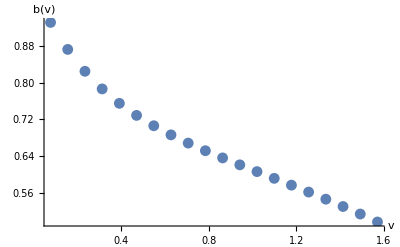

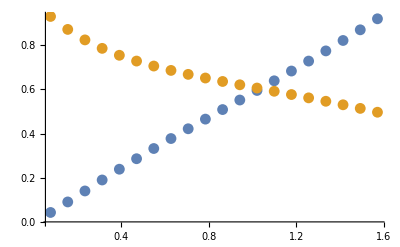

```mathematica
ListPlot[valuesA,PlotRange->Full,AxesLabel->{"v","a(v)"}] 
ListPlot[valuesB,PlotRange->Full,AxesLabel->{"v","b(v)"}]
ListPlot[{valuesA,valuesB},PlotRange->Full]
```

It would seem that a(v) is almost linear but b(v) seems to have a slight inflection indicating maybe the need for a 3rd order polynomial?

{a→0.00118554,b→0.599188,c→-0.012787}

{a→0.977767,b→-0.748114,c→0.555383,d→-0.175846}

0.00118554+0.599188 x-0.012787 x^2

0.977767-0.748114 x+0.555383 x^2-0.175846 x^3

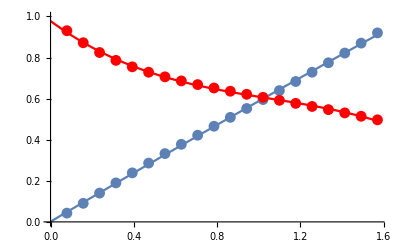

```mathematica
modelA=a+b*x+c*x^2;
modelB = a + b*x + c*x^2+d*x^3;
fittingA = FindFit[valuesA,modelA,{a,b,c},x]
fittingB = FindFit[valuesB,modelB,{a,b,c,d},x]
modelA/.fittingA
modelB/.fittingB
Show[
ListPlot[valuesA], Plot[modelA/.fittingA,{x,0,π/2}],
ListPlot[valuesB,PlotStyle->Red], Plot[modelB/.fittingB,{x,0,π/2},PlotStyle->Red],
PlotRange->{{0,π/2},{0,1}}
]
```

```mathematica
functionA = Function[{x},Evaluate[modelA/.fittingA]]
functionB = Function[{x},Evaluate[modelB/.fittingB]]
G[u_,v_]:= v*Exp[-functionA[v]*u^functionB[v]];
Plot3D[G[u,v],{u,0,10},{v,0,π/2},PlotRange->Full,AxesLabel->{"u","v","G[u,v]"}]
```

Function[{x},0.00118554+0.599188 x-0.012787 x^2]

Function[{x},0.977767-0.748114 x+0.555383 x^2-0.175846 x^3]

-Graphics3D-

```mathematica
Plot3D[{F[u,v],G[u,v]},{u,0,rangeU},{v,0,π/2},PlotRange->Full,AxesLabel->{"u","v","F[u,v]"}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[G[u,v]-F[u,v]],{u,0,rangeU},{v,0,π/2},PlotRange->Full,AxesLabel->{"u","v","|G[u,v]-F[u,v]|"}]
```

-Graphics3D-

```mathematica
Plot3D[100*(G[u,v]/F[u,v]-1.0),{u,0,rangeU},{v,0,π/2},PlotRange->Full,AxesLabel->{"u","v","relative error %"}]
```

-Graphics3D-

```mathematica
Plot3D[100*Abs[G[u,v]/F[u,v]-1.0],{u,0,rangeU},{v,0,π/2},PlotRange->Full,AxesLabel->{"u","v","Relative error %"},ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

# Part 2: Surface Radiance Integral

Equation 15 in the paper gives us the radiance integral for a surface, accounting for single-scattering by an isotropic participating medium:

	L_(p,a)=∫_(Ω_(2π)) L_a(γ'(θ_s,ω_i),T_sp,∞,β)f_r(θ_i,ϕ_i,θ_v,ϕ_v) cosθ_i dω_i     (15)

where:
L_a is the airlight integral from eq. 9
f_r is the surface’s BRDF
γ' is the angle between the incoming direction and the light source


Using eq. 12 in place of L_a, the integral from eq. 15 transforms into:

	L_(p,a)=∫_(Ω_(2π)) A_0(T_sp,γ',β)[F(A_1(T_sp,γ'),π/2) - F(A_1(T_sp,γ'),γ'/2)]  f_r(θ_i,ϕ_i,θ_v,ϕ_v) cosθ_i dω_i

Remember that:

	A_0(T_sp,γ',β)=(β^2 I_0 e^-T_spcosγ')/(2π T_sp sinγ')
and	A_1(T_sp,γ')=T_sp sinγ'

So:

	L_(p,a)=(β^2 I_0)/(2π T_sp) ∫_(Ω_(2π)) e^-T_spcosγ'/sinγ'[F(T_sp sinγ',π/2) -F(T_sp sinγ',γ'/2)] f_r(θ_i,ϕ_i,θ_v,ϕ_v) cosθ_i dω_i	(15’)
	
We can write the general term G as:

	G(T_sp,θ'_s)=∫_(Ω_(2π)) e^-T_spcosγ'/sinγ'[F(T_sp sinγ',π/2) -F(T_sp sinγ',γ'/2)] f_r(θ_i,ϕ_i,θ_v,ϕ_v) cosθ_i dω_i

Finally G is only dependent on θ'_s since cos(γ'(θ'_s,ω_i))=cosθ_i cosθ'_s+sinθ_i sinθ_s cosϕ_i

	In the case of diffuse reflection, θ'_s is the angle between the source and the surface’s normal
	In the case of specular reflection, θ'_s is chosen to be the angle between the source and the reflected view vector


In the paper, the BRDF is the Phong model which is simply f_r(θ_i,ϕ_i,θ_v,ϕ_v) =k_s.cos^n(θ_i) and thus:

	G_Phong_n(T_sp,θ'_s)= ∫_(Ω_(2π)) e^-T_spcosγ'/sinγ'[F(T_sp sinγ',π/2) -F(T_sp sinγ',γ'/2)]cos^n θ_i dω_i      (16)
	
with the special case n=1 for the diffuse lambert reflection. 

Equation 16 is then our simplification goal.
I’m using a side program to generate several G_n tables for different values of n that will be imported.

### Importing the tables

```mathematica
SetDirectory[NotebookDirectory[]];
rawTable = BinaryReadList["./TableG0.double","Real64"];
Short[rawTable,4]
```

{2.4132,2.16568,1.87974,1.64991,1.45799,1.29417,1.15315,1.03065,0.922428,«4078»,0.0429356,-0.00479737,0.000101052,0.00534641,0.0108971,0.0172855,0.0256823,0.033813,0.0413222}

```mathematica
maxU=5;
tableTest=Table[{maxU*Mod[i,64]/63,π/2*Floor[i/64] / 63,rawTable[[1+i]]},{i,0,64*64-1,1}];
ListPlot3D[tableTest,PlotRange->{0,10},AxesLabel->{"T_sp","θ_s"}]
```

-Graphics3D-

### Fitting

```mathematica
ColorData["TemperatureMap"]
```

ColorDataFunction[…]

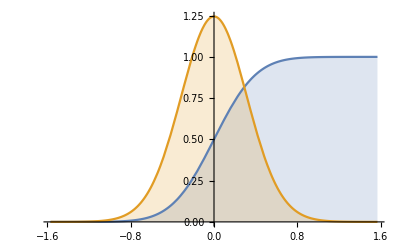

```mathematica
κ=10;
Plot[{CDF[VonMisesDistribution[0.0,κ]][x], PDF[VonMisesDistribution[0.0,κ]][x]},{x,-π/2,π/2},Filling->Axis]
```

```mathematica
Clear[F]
F[u_?NumericQ, v_?NumericQ] := NIntegrate[Exp[-u*Tan[ξ]], {ξ,0,ArcCos[v]}]
```

```mathematica
Plot3D[F[u, v], {u,0,10},{v, 0, 1},PlotRange->Full,AxesLabel->{"u","v","F[u,v]"}]
```

-Graphics3D-

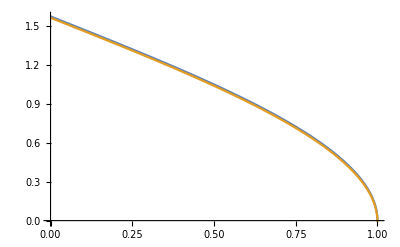

```mathematica
Plot[{F[0,v],ArcCos[v]-0.01},{v,0,1}]
```

We need to find a nice fit for Acos[v]...

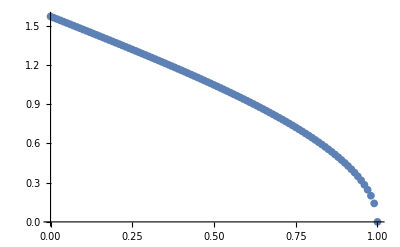

```mathematica
dataAcos=Table[{i/100,ArcCos[i/100]},{i,0,100}];
ListPlot[dataAcos,PlotRange->Full]
```

Function[x,1/2 π (1-x)^0.565112]

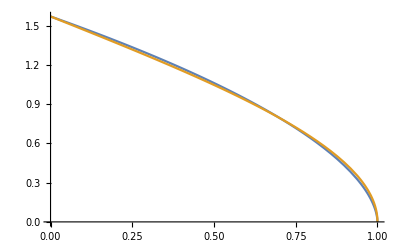

```mathematica
(*modelAcos[v_]:=π/2*Sqrt[1-v];*)
modelAcos=π/2*(1-x)^a;
modelAcos=Function[x,Evaluate[modelAcos/. FindFit[dataAcos,modelAcos,{{a,0.5}},x,Method->"PrincipalAxis"]]]
Plot[{modelAcos[v],ArcCos[v]},{v,0,1},PlotRange->{0,π/2}]
```

21

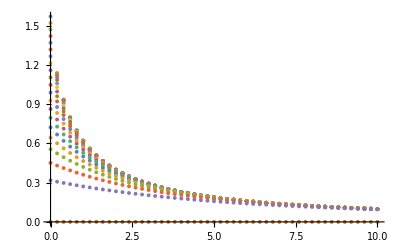

```mathematica
curvesCount=20;
curvesU=Table[{u,F[u,v]},{v,0,1,1/curvesCount},{u,0,10,0.2}];
Length[curvesU]
ListPlot[curvesU,PlotRange->Full]
```

Testing fitting of model “Acos[v] e^(a*u^b)” with our first curve:

Function[u,1.5708 ⅇ^(-0.91212 u^0.523829)]

1.5708

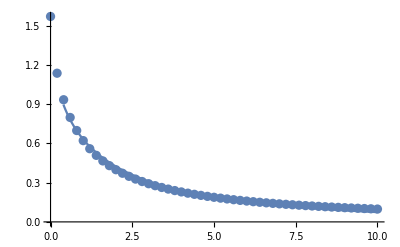

```mathematica
modelCurveU[v_]:=modelAcos[v]*Exp[a*u^b];
fit0 = FindFit[curvesU[[1]],modelCurveU[0],{{a,-1},{b,1}},u,Method->"PrincipalAxis"];
functionU0=Function[u,Evaluate[modelCurveU[0]/.fit0]]
functionU0[0]
Show[ListPlot[curvesU[[1]],PlotRange->{0,π/2}],Plot[functionU0[u],{u,0,10}]]
```

Now, do that for all curves and generate a list of {a,b} fitting parameters...

```mathematica
fits=Table[FindFit[curvesU[[i]],modelCurveU[(i-1)/curvesCount],{{a,-1},{b,1}},u,Method->"PrincipalAxis"],{i,1,curvesCount}];
AppendTo[fits,{a->0,b->1.4}];(* special case for last curve *)
MatrixForm[fits]
```

(a→-0.91212 | b→0.523829
a→-0.881769 | b→0.536455
a→-0.850607 | b→0.549669
a→-0.81935 | b→0.562816
a→-0.788133 | b→0.575742
a→-0.756873 | b→0.588487
a→-0.72542 | b→0.601153
a→-0.693589 | b→0.613873
a→-0.66117 | b→0.626808
a→-0.627922 | b→0.640149
a→-0.593566 | b→0.654131
a→-0.557766 | b→0.669058
a→-0.520106 | b→0.685335
a→-0.48005 | b→0.703542
a→-0.43688 | b→0.724551
a→-0.389584 | b→0.749786
a→-0.33664 | b→0.781811
a→-0.275565 | b→0.825983
a→-0.20177 | b→0.896511
a→-0.105045 | b→1.05546
a→0 | b→1.4)

```mathematica
Manipulate[Show[Plot[Function[u,modelCurveU[(i-1)/curvesCount]/.fits[[i]]][u],{u,0,10},PlotRange->{0,π/2}],ListPlot[curvesU[[i]]]],{i,1,curvesCount+1,1}]
```

Now let’s try and fit {a,b} using some polynomials

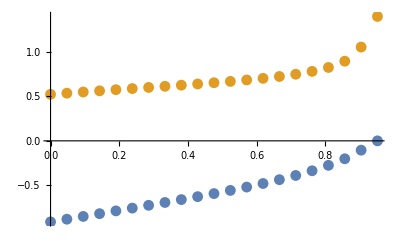

```mathematica
coeffsA=Table[{(i-1)/(curvesCount+1),a/.fits[[i]]},{i,1,curvesCount+1}];
coeffsB=Table[{(i-1)/(curvesCount+1),b/.fits[[i]]},{i,1,curvesCount+1}];
ListPlot[{coeffsA,coeffsB}]
```

Let’s use 3nd order for both a and b...

Function[x,-0.923137+0.895017 x-0.979522 x^2+1.09125 x^3]

Function[x,0.549903-0.715014 x+6.29063 x^2-13.0325 x^3+8.52774 x^4]

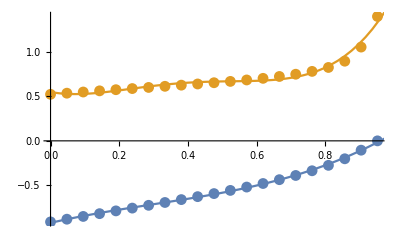

```mathematica
modelA=a+b*x+c*x^2+d*x^3;
modelB=a+b*x+c*x^2+d*x^3+e*x^4;
fitA=Function[x,Evaluate[modelA/.FindFit[coeffsA,modelA,{a,b,c,d},x,Method->"Automatic"]]]
fitB=Function[x,Evaluate[modelB/.FindFit[coeffsB,modelB,{a,b,c,d,e},x,Method->"Automatic"]]]
Show[ListPlot[{coeffsA,coeffsB}],Plot[{fitA[v],fitB[v]},{v,0,1}]]
```

We now have our complete function F2 :

```mathematica
F2[u_,v_]:=modelAcos[v]*Exp[fitA[v]*u^fitB[v]]
Plot3D[{F[u,v],F2[u,v]},{u,0,10},{v,0,1},PlotRange->Full,AxesLabel->{"u","v","F[u,v]"}]
```

-Graphics3D-